## Задача 1. Атом водорода

Как известно, уравнение на радиальную функцию атома водорода с квантовыми числами l, m (приравниваем 2 E*R[r]):

```mathematica
eq=R''[r]+2/r*R'[r]+(-l*(l+1)/r^2+2/r)*R[r]
```

(-2/r^2+2/r) R[r]+(2 R'[r])/r+R''[r]

Возьмем конкретное l и решим уравнение при ряде значений энергии

```mathematica
Clear[l, EE];
l=1;
EE = 1/2*{0.25, 0.5, 1.0};
```

Divide::infy: Infinite expression 1/0 encountered.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -C[2] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

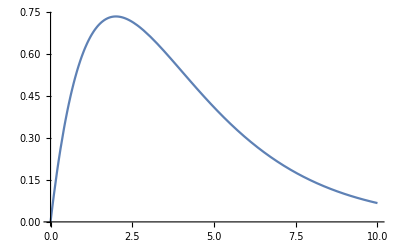

```mathematica
Clear[EE];
EE=1/8;
sol=DSolve[{eq==2*R[r]*EE,R[0]==0,R'[0]==1},R[r],r][[1]];
Plot[R[r]/.sol,{r,0,10}]
```

Divide::infy: Infinite expression 1/0 encountered.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -C[2] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

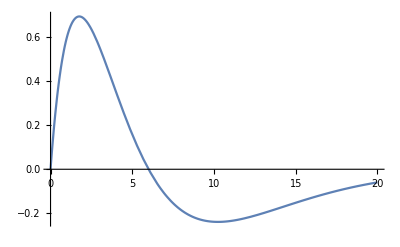

```mathematica
Clear[EE];
EE=1/18;
sol=DSolve[{eq==2*R[r]*EE,R[0]==0,R'[0]==1},R[r],r][[1]];
Plot[R[r]/.sol,{r,0,20}]
```

```mathematica
Clear[EE];
EE=1/19;
sol=DSolve[{eq==2*R[r]*EE,R[0]==0,R'[0]==1},R[r],r][[1]];
Plot[R[r]/.sol,{r,0,200}]
```

-Graphics-

В целом, все работает, пусть даже и ругается. Его можно понять и остается только простить.

## Задача 2. q^2=-1

```mathematica
q/:
q^(m_):=-1*q^(m-2)/;m≥2
```

```mathematica
??q
```

Global`q

q^m_^:=-q^(m-2)/;m≥2

```mathematica
q^2+2q^4+q^3
```

1-q

## Задача 3. Алгебра кватернионов

```mathematica
Clear[Quaternion];
Quaternion/:
Quaternion[a1_,b1_,c1_,d1_]**Quaternion[a2_,b2_,c2_,d2_]:=Quaternion[
a1*a2-b1*b2-c1*c2-d1*d2,
b1*a2+a1*b2+c1*d2-d1*c2,
c1*a2+a1*c2-b1*d2+d1*b2,
d1*a2+a1*d2+b1*c2-c1*b2
];
Quaternion/:
Quaternion[a1_,b1_,c1_,d1_]*m_:=Quaternion[a1*m,b1*m,c1*m,d1*m];
Quaternion/:
Quaternion[a1_,b1_,c1_,d1_]+Quaternion[a2_,b2_,c2_,d2_]:=Quaternion[
a1+a2,
b1+b2,
c1+c2,
d1+d2
];
```

```mathematica
BeautifulQF[Quaternion[a_,b_,c_,d_]]:=a+b*i+c*j+d*k;
```

```mathematica
q1 = Quaternion[a1,b1,c1,d1];
q2 = Quaternion[a2,b2,c2,d2];
q3= Quaternion[a3,b3,c3,d3];
```

```mathematica
q1**q2+q3//BeautifulQF
```

a1 a2+a3-b1 b2-c1 c2-d1 d2+(a2 b1+a1 b2+b3-c2 d1+c1 d2) i+(a2 c1+a1 c2+c3+b2 d1-b1 d2) j+(-b2 c1+b1 c2+a2 d1+a1 d2+d3) k

```mathematica
q1**q2-q2**q1//BeautifulQF
```

(-2 c2 d1+2 c1 d2) i+(2 b2 d1-2 b1 d2) j+(-2 b2 c1+2 b1 c2) k

```mathematica
(q1+q2)**q3//BeautifulQF
```

(a1+a2) a3-(b1+b2) b3-(c1+c2) c3-(d1+d2) d3+(a3 (b1+b2)+(a1+a2) b3-c3 (d1+d2)+(c1+c2) d3) i+(a3 (c1+c2)+(a1+a2) c3+b3 (d1+d2)-(b1+b2) d3) j+(-b3 (c1+c2)+(b1+b2) c3+a3 (d1+d2)+(a1+a2) d3) k

Попытка закодить кватернионы правилами замены (через i,j,k) успехом, к сожалению, не увенчалась. Судя по тому, что вольфрамовская родная либа построена +- по тому же принципу, что и реализация выше, это вообще не факт, что возможно. Возникают проблемы с некоммутативным умножением, правилами работы с произведением констант перед базисными элементами.

## Задача 4. Уравнения Гамильтона

По заданному гамильтониану в d-мерном пространстве найдем 2d уравнений Гамильтона.

```mathematica
HamiltonEq[H_,coord_]:=
Block[{n,i,equations},
n=Length[coord];
equations=Table[0,n];
For[i=1,i≤ n,i++,
equations[[i]]={
D[coord[[i,2]][t],t]==-D[H,coord[[i,1]][t]],
D[coord[[i,1]][t],t]==D[H,coord[[i,2]][t]]
};
];
Return[equations]
];
```

```mathematica
H1=1/(2m)*p[t]^2+U[q[t]];
H2=1/(2m[1])*p[1][t]^2+1/(2m[2])*p[2][t]^2+U[q[1][t]];
```

```mathematica
HamiltonEq[H1,{{q,p}}]//TableForm
```

p'[t]==-U'[q[t]] | q'[t]==p[t]/m

```mathematica
HamiltonEq[H2,{{q[1],p[1]},{q[2],p[2]}}]//TableForm
```

p[1]'[t]==-U'[q[1][t]] | q[1]'[t]==(p[1][t])/m[1]
p[2]'[t]==0 | q[2]'[t]==(p[2][t])/m[2]

## Задача5. Уравнения Гамильтона-Якоби

По заданному гамильтониану в d-мерном пространстве выпишем уравнение Гамильтона-Якоби на функцию S.

```mathematica
Clear[HamJacEq,n,i];
HamJacEq[H_,coord_]:=
Block[{n,i,equation,newc,rule0,rule1,rule2,SS},
n=Length[coord];
newc=StringRiffle[Table[coord[[i,1]],{i,1,n}],","];
SS=ToExpression["S["<>newc<>",t]"];
rule1=Table[coord[[i,2]][t]->D[SS,coord[[i,1]]],{i,1,n}];
rule0=Table[coord[[i,1]][t]->coord[[i,1]],{i,1,n}];
rule2=Table[coord[[i,1]]->coord[[i,1]][t],{i,1,n}];
equation=H/.rule0/.rule1;
equation=equation+D[SS,t];
Return[equation/.rule2]
];
```

```mathematica
HamJacEq[H1,{{q,p}}]
```

U[q[t]]+S^(0,1)[q[t],t]+((S^(1,0)[q[t],t])^2)/(2 m)

```mathematica
HamJacEq[H2,{{q[1],p[1]},{q[2],p[2]}}]
```

U[q[1][t]]+S^(0,0,1)[q[1][t],q[2][t],t]+((S^(0,1,0)[q[1][t],q[2][t],t])^2)/(2 m[2])+((S^(1,0,0)[q[1][t],q[2][t],t])^2)/(2 m[1])